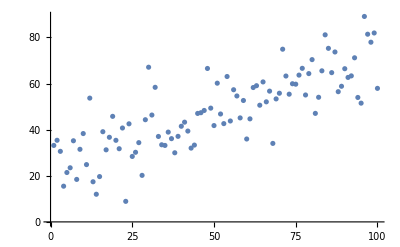

```mathematica
Y = Table[6 *x - Log[x]*2 + 20, {x, 0.1,10,0.1}];
Data = Transpose[{Table[icounter, {icounter, 1, Length[Y]}], Y}];
noise=RandomVariate[NormalDistribution[0,10],Length@Data];
FirstDataSet = Transpose[{(Transpose@Data)[[1]],(Transpose@Data)[[2]] + noise}];
ListPlot[FirstDataSet]
```

```mathematica
Y = Table[-6 * x +50 + Exp[x +0.2]/x/70 - (x - 6) * (x - 6), {x, 0.1,10,0.1}];
Data = Transpose[{Table[icounter, {icounter, 1, Length[Y]}], Y}];
SecondDataSet = AddNoise[Data, 4];
ListPlot[SecondDataSet]
ListPlot[Data]
```

```mathematica
LinearModel[DataSet_]:= Module[
{Answers,DataVectors,result}
,
Answers = Transpose[{Transpose[DataSet][[Length[DataSet[[1]]]]]}];
(*DataVectors = Transpose[{Transpose[DataSet][[1]], ConstantArray[1,Length[DataSet]]}];*)

DataVectors = Transpose[  Delete[Transpose[DataSet], Length[DataSet[[1]]]]  ];
result = PseudoInverse[DataVectors].Answers
];

TransformParametersOne[DataSet_]:= Module[
{Answers,DataVectors,result}
,
Answers = Transpose[DataSet][[Length[DataSet[[1]]]]];
result= Transpose[{Transpose[DataSet][[1]], ConstantArray[1,Length[DataSet]], Answers}]

]
TransformParametersSecond[DataSet_]:= Module[
{Answers,DataVectors,result,xx}
,
Answers = Transpose[DataSet][[Length[DataSet[[1]]]]];
xx = Transpose[DataSet][[1]];
result= Transpose[{xx, N@Sin[xx/10],ConstantArray[1,Length[DataSet]], Answers}]

]
TransformParametersThird[DataSet_]:= Module[
{Answers,DataVectors,result,xx}
,
Answers = Transpose[DataSet][[Length[DataSet[[1]]]]];
xx = Transpose[DataSet][[1]];
result= Transpose[{xx, N@Exp[xx/10]/xx,xx*xx,ConstantArray[1,Length[DataSet]], Answers}]

]
```

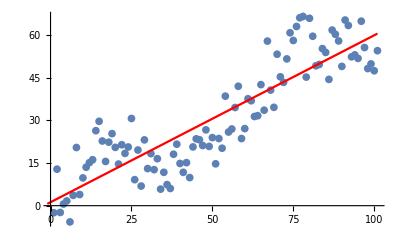

```mathematica
Show[ListPlot[FirstDataSet], Plot[LinearModel[TransformParametersOne@FirstDataSet][[1]] * x + LinearModel[TransformParametersOne@FirstDataSet][[2]], {x,-1,101}, PlotStyle->{Red}]]
```

```mathematica
FirstDataSet = ReadList["C:\\Users\\admin\\Desktop\\krs\\FirstDataSet.txt",{Number,Number}];
SecondDataSet = ReadList["C:\\Users\\admin\\Desktop\\krs\\SecondDataSet.txt",{Number,Number}];
```

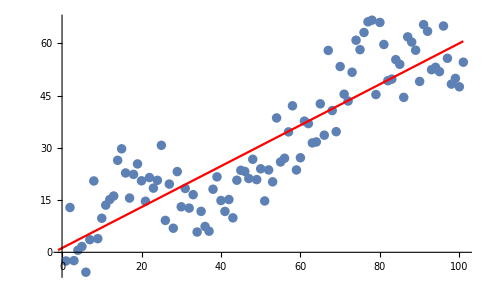

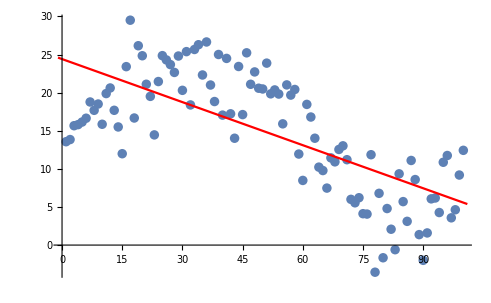

```mathematica
Show[ListPlot[FirstDataSet], Plot[LinearModel[FirstDataSet][[1]] * x + LinearModel[FirstDataSet][[2]], {x,-1,101}, PlotStyle->{Red}]]
Show[ListPlot[SecondDataSet], Plot[LinearModel[SecondDataSet][[1]] * x + LinearModel[SecondDataSet][[2]], {x,-1,101}, PlotStyle->{Red}]]
```

Modeli naideny

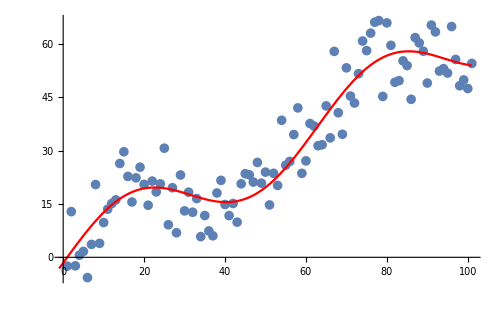

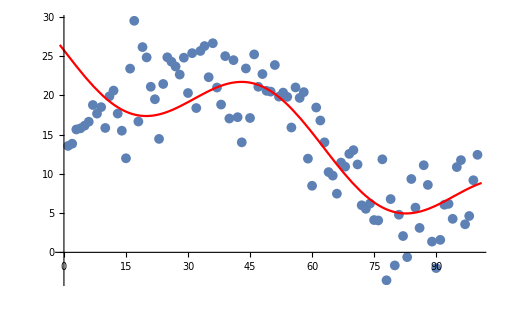

```mathematica
FirstModel = LinearModel[TransformParametersSecond@FirstDataSet];
SecondModel = LinearModel[TransformParametersSecond@SecondDataSet];
Print["Modeli naideny"];
Show[ListPlot[FirstDataSet], Plot[FirstModel[[1]] * x + Sin[x/10]*FirstModel[[2]] +FirstModel[[3]], {x,-1,101}, PlotStyle->{Red}]]
Show[ListPlot[SecondDataSet], Plot[SecondModel[[1]] * x + Sin[x/10] *SecondModel[[2]] + SecondModel[[3]], {x,-1,101}, PlotStyle->{Red}]]
```

Modeli naideny

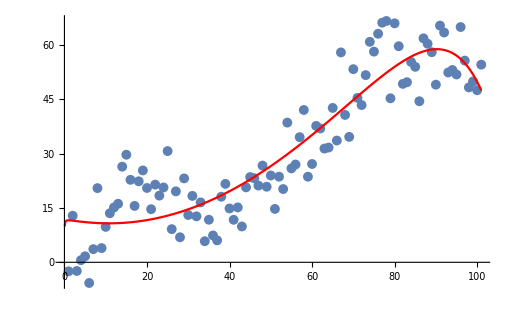

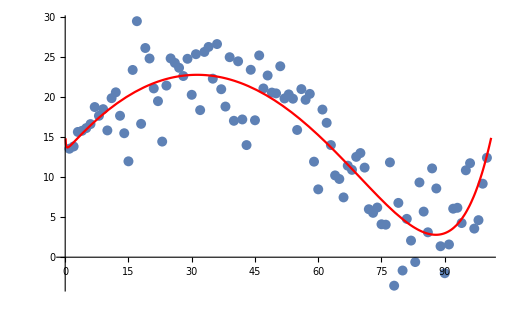

```mathematica
FirstModel = LinearModel[TransformParametersThird@FirstDataSet];
SecondModel = LinearModel[TransformParametersThird@SecondDataSet];
Print["Modeli naideny"];
Show[ListPlot[FirstDataSet], Plot[FirstModel[[1]] * x + Exp[x/10]/x*FirstModel[[2]] + x*x*FirstModel[[3]]   +FirstModel[[4]], {x,0.1,101}, PlotStyle->{Red}]]
Show[ListPlot[SecondDataSet], Plot[SecondModel[[1]] * x + Exp[x/10]/x*SecondModel[[2]] + x*x*SecondModel[[3]]   +SecondModel[[4]], {x,0.1,101}, PlotStyle->{Red}]]
```